## Copyright notice

timing-tests.nb

Copyright 2017 Ben Niehoff
ben.niehoff@gmail.com

This program is free software: you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
GNU General Public License for more details.

You should have received a copy of the GNU General Public License
along with this program.  If not, see <http://www.gnu.org/licenses/>.

## Initial setup

Quit[] is just the easiest way to clean the slate in case something goes horribly wrong

```mathematica
Quit[]
```

### Start here

Make sure you have created a directory at “./data”, or else the tests below will fail to write data files!

```mathematica
SetDirectory[NotebookDirectory[]]
```

### Load xPerm

```mathematica
<<xAct`xPerm`
```

### Define some useful shorthand:

```mathematica
canonicalPerm=xAct`xPerm`Private`MLCanonicalPerm
```

xAct`xPerm`Private`MLCanonicalPerm

Note:  xPerm overwrites the native Cycles[{{}}] function, so we have to use System`Cycles[]

```mathematica
SCycles=System`Cycles
```

System`Cycles

### Load canonicalization.m

```mathematica
SetDirectory[NotebookDirectory[]]
<<FileNameJoin[{%,"canonicalization.m"}]
```

### Checking improvedButlerPortugal syntax

```mathematica
group=PermutationGroup[{
SCycles[{{1,2}}],SCycles[{{2,3}}],SCycles[{{3,4}}],SCycles[{{4,5}}],
SCycles[{{5,6}}],SCycles[{{6,7}}],SCycles[{{7,8}}]
}];
group=PermutationGroup[{
SCycles[{{1,2},{5,6}}],SCycles[{{3,4},{5,6}}],SCycles[{{1,3},{2,4}}]
}];
length=6;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata]
labeldata={
{1,2,3,4,5,6,7,8,9,10},
{0,0,0,0,0,0,0,0,0,0}
};
labeldata={
{1,1,1,1,5,6},
{2,2,2,2,0,0}
};
MatrixForm[labeldata]
initialconfig=Join[RandomSample[Range[8]],{9,10}];
initialconfig=Join[RandomSample[Range[4]],{5,6}]
```

{-1,-1,-2,-2,0,0}

(1 | 1 | 1 | 1 | 5 | 6
2 | 2 | 2 | 2 | 0 | 0)

{3,4,2,1,5,6}

```mathematica
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
```

{0,0,0,0,0,0}

```mathematica
Table[
initialconfig=Join[RandomSample[Range[8]],{9,10}];
First@AbsoluteTiming@improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata],
50];
Total[%]/50.
```

0.0000992739

### Checking xPerm syntax

```mathematica
group=PermutationGroup[{
SCycles[{{1,2}}],SCycles[{{2,3}}],SCycles[{{3,4}}],SCycles[{{4,5}}],
SCycles[{{5,6}}],SCycles[{{6,7}}],SCycles[{{7,8}}]
}];
group=PermutationGroup[{SCycles[{{1,2},{3,4}}]}];
length=4;
initialconfig=Join[RandomSample[Range[8]],{9,10}];
initialconfig={1,2,3,4}
sgsswitch=1;
generators=Flatten@Sort@listifyGenerators[group,length];
base=Range[length-2];
frees={};
dummysetspec={2};
dummysets=Flatten@{{1,2}};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
```

{1,2,3,4}

```mathematica
canonicalPerm[initialconfig,length,sgsswitch,base,generators,frees,
dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
```

Images[{0,0}]

```mathematica
Table[
initialconfig=Join[RandomSample[Range[8]],{9,10}];
First@AbsoluteTiming@canonicalPerm[initialconfig,length,sgsswitch,base,generators,frees,
dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets],
50];
Total[%]/50.
```

0.000512534

### Checking Mathematica native syntax

```mathematica
group=PermutationGroup[{
SCycles[{{1,2}}],SCycles[{{2,3}}],SCycles[{{3,4}}],SCycles[{{4,5}}],
SCycles[{{5,6}}],SCycles[{{6,7}}],SCycles[{{7,8}}]
}];
length=10;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
initialconfig=TensorTranspose[A,RandomSample[Range[8]]];
Block[{$Assumptions={A∈Arrays[ConstantArray[dim,8],Reals,Symmetric[All]]}},
Table[
First@AbsoluteTiming@TensorReduce[TensorTranspose[A,RandomSample[Range[8]]]],
10]]
```

{0.00579939,0.000984616,0.00131651,0.00075159,0.00123241,0.00098995,0.000698667,0.000758154,0.00079877,0.000790154}

It looks like Mathematica is not smart enough to avoid recomputing the base and strong generating set :(

Let’s try actually setting the global $Assumptions:

```mathematica
$Assumptions={A∈Arrays[ConstantArray[dim,8],Reals,Symmetric[Range[8]]]}
Table[
First@AbsoluteTiming@TensorReduce[TensorTranspose[A,RandomSample[Range[8]]]],
10]
```

{A∈Arrays[{dim,dim,dim,dim,dim,dim,dim,dim},Reals,Symmetric[{1,2,3,4,5,6,7,8}]]}

{0.000646154,0.00105436,0.00107036,0.00086236,0.000985026,0.000664616,0.00057559,0.000530872,0.000659693,0.000849231}

This does not help.  Mathematica makes no attempt to remember the group.

```mathematica
$Assumptions={}
```

{}

Can we take advantage of Listable, maybe?

```mathematica
Attributes[TensorReduce]
```

{Protected,ReadProtected}

```mathematica
trials=50;
Block[{$Assumptions={A∈Arrays[ConstantArray[dim,8],Reals,Symmetric[Range[8]]]}},
With[{input=Total@Table[TensorTranspose[A,RandomSample[Range[8]]],trials]},
AbsoluteTiming@TensorReduce[input]
]]
First[%]/N[trials]
```

{0.0263627,50 A}

0.000527254

### Utility functions

#### Building symmetric groups by SGS

The simplest way is to use a List as input, then we can use all the features of Range

```mathematica
buildSymmetricGroup[list_List]:=
PermutationGroup[Map[SCycles[{#}]&,Partition[list,2,1]]];
```

```mathematica
buildSymmetricGroup[Range[1]]
```

PermutationGroup[{}]

#### Generating plots

```mathematica
buildListPlot[data_,plotFunction_,color_,marker_]:=
plotFunction[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},
Filling->{1->{3}},FillingStyle->Thick,
PlotStyle->color,
PlotMarkers->{Null,marker,Null}];
```

#### Building Riemann symmetry groups

This test is a little more complex.  We need a function to build a Riemann symmetry group out of n Riemann tensors

```mathematica
buildRiemannGroup[numR_]:=
Module[{length,indices},
length=4*numR+2;
indices=Range[length-2];
PermutationGroup[
Join[
Map[SCycles[{{#⟦1⟧,#⟦2⟧},{length-1,length}}]&,Partition[indices,2]],
Map[SCycles[{{#⟦1⟧,#⟦3⟧},{#⟦2⟧,#⟦4⟧}}]&,Partition[indices,4]],
Map[SCycles[{{#⟦1⟧,#⟦5⟧},{#⟦2⟧,#⟦6⟧},{#⟦3⟧,#⟦7⟧},{#⟦4⟧,#⟦8⟧}}]&,
Partition[indices,8,4]]
]
]];
```

```mathematica
buildRiemannGroup[1]
```

PermutationGroup[{System`Cycles[{{1,2},{5,6}}],System`Cycles[{{3,4},{5,6}}],System`Cycles[{{1,3},{2,4}}]}]

```mathematica
buildRiemannGroup[3]
```

PermutationGroup[{System`Cycles[{{1,2},{13,14}}],System`Cycles[{{3,4},{13,14}}],System`Cycles[{{5,6},{13,14}}],System`Cycles[{{7,8},{13,14}}],System`Cycles[{{9,10},{13,14}}],System`Cycles[{{11,12},{13,14}}],System`Cycles[{{1,3},{2,4}}],System`Cycles[{{5,7},{6,8}}],System`Cycles[{{9,11},{10,12}}],System`Cycles[{{1,5},{2,6},{3,7},{4,8}}],System`Cycles[{{5,9},{6,10},{7,11},{8,12}}]}]

#### Constructing pairwise totally symmetric split groups

```mathematica
buildBlockSymmetricGroup[start_,numblocks_,blocksize_]:=
With[{list=Range[start,start+numblocks*blocksize-1]},
PermutationGroup[
Map[
SCycles[Transpose[{#⟦1;;blocksize⟧,#⟦blocksize+1;;2*blocksize⟧}]]&,
Partition[list,2*blocksize,blocksize]
]]];
```

```mathematica
buildBlockSymmetricGroup[1,4,2]
```

PermutationGroup[{System`Cycles[{{1,3},{2,4}}],System`Cycles[{{3,5},{4,6}}],System`Cycles[{{5,7},{6,8}}]}]

```mathematica
Block[{timings,group,length,generators,signedgens,blocksize=3,numblocks=8,range},
range=blocksize*numblocks;
group=Join[
buildBlockSymmetricGroup[1,numblocks,blocksize],
buildBlockSymmetricGroup[1+range,numblocks,blocksize]
];
length=2*range+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,2*range],Reals,signedgens]}},
With[{initialconfig=TensorContract[A,
Transpose[{RandomSample@Range[range],range+RandomSample@Range[range]}]
]},
{initialconfig,TensorReduce[initialconfig]}
]
]
]
```

{TensorContract[A,{{1,45},{2,30},{3,31},{4,37},{5,32},{6,25},{7,48},{8,39},{9,36},{10,38},{11,46},{12,34},{13,27},{14,44},{15,28},{16,33},{17,41},{18,47},{19,26},{20,35},{21,42},{22,40},{23,29},{24,43}}],TensorContract[A,{{1,37},{2,32},{3,25},{4,26},{5,35},{6,42},{7,27},{8,44},{9,28},{10,40},{11,29},{12,43},{13,45},{14,30},{15,31},{16,33},{17,41},{18,47},{19,38},{20,46},{21,34},{22,48},{23,39},{24,36}}]}

## Demo test: Symmetrizing free indices

### Data for Mathematica built-in functions

```mathematica
Module[
{numindicesrange=Range[1,301,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,signedgens},
group=buildSymmetricGroup[Range[#1]];
length=#1+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,#1],Reals,signedgens]}},
timings=Table[
With[{initialconfig=TensorTranspose[A,RandomSample[Range[#1]]]},
First@AbsoluteTiming@TensorReduce[initialconfig]
],
trialsperrun]
];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/sym-frees-builtin.data"
```

### Data for xPerm

```mathematica
Module[
{numindicesrange=Range[1,301,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets},
group=buildSymmetricGroup[Range[#1]];
length=#1+2;
base=Range[#1];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees=Range[#1];
dummysetspec={0};
dummysets=Flatten@{{}};
dummysetsigns={};
repeatsetspec={0};
repeatsets=Flatten@{{}};
timings=Table[
With[{initialconfig=Join[RandomSample[Range[#1]],{#1+1,#1+2}]},
First@AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/sym-frees-xperm.data"
```

### Data for improved BP

```mathematica
Module[
{numindicesrange=Range[1,301,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,slotdata,subgroups,labeldata},
group=buildSymmetricGroup[Range[#1]];
length=#1+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Range[length],
ConstantArray[0,length]
};
timings=Table[
With[{initialconfig=Join[RandomSample[Range[#1]],{#1+1,#1+2}]},
First@AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/sym-frees-improved.data"
```

### Generating plots

First let’s read in the data from the files:

```mathematica
symFreesBuiltin=<<"data/sym-frees-builtin.data";
symFreesxPerm=<<"data/sym-frees-xperm.data";
symFreesImproved=<<"data/sym-frees-improved.data";
```

Now let’s see if we can create a plot with all three

```mathematica
buildListPlot[symFreesBuiltin,ListLogPlot,GrayLevel[0.4],"○"]
```

-Graphics-

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{symFreesBuiltin,symFreesxPerm,symFreesImproved},
{GrayLevel[0.3],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

```mathematica
logFitSymFreesxPerm=Fit[MapAt[Log,
Select[symFreesxPerm,#[[1]]≥100&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-21.4131+3.60727 Log[x]

```mathematica
logFitSymFreesImproved=Fit[MapAt[Log,
Select[symFreesImproved,#[[1]]≥100&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-15.6304+2.28322 Log[x]

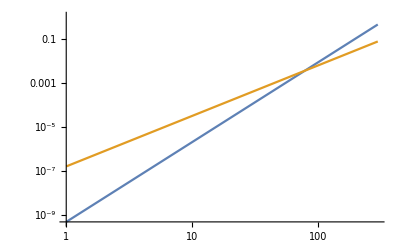

```mathematica
With[{curves=Exp@{logFitSymFreesxPerm,logFitSymFreesImproved}},
LogLogPlot[curves,{x,1,300}]]
```

```mathematica
Show[
Join[
MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{symFreesBuiltin,symFreesxPerm,symFreesImproved},
{GrayLevel[0.5],Hue[0.06,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
{With[{curves=Exp@{logFitSymFreesxPerm,logFitSymFreesImproved}},
LogPlot[curves,{x,1,300},
PlotStyle->{{Hue[0.06,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]
]}],
PlotRange->{Log[10^-5],Log[1.5]},AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

## Demo test: Dummy indices with cyclic symmetry

### Data for Mathematica built-in functions

```mathematica
Module[
{numindicesrange=Range[1,201,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,signedgens},
group=PermutationGroup[{SCycles[{Range[#1]}],SCycles[{Range[#1+1,2*#1]}]}];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,2*#1],Reals,signedgens]}},
timings=Table[
With[{initialconfig=TensorContract[A,
Transpose[{RandomSample@Range[#1],
#1+RandomSample@Range[#1]}]]},
First@AbsoluteTiming@TensorReduce[initialconfig]
],
trialsperrun]];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/cyclic-dummies-builtin.data"
```

### Data for xPerm

```mathematica
Module[
{numindicesrange=Range[1,61,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets},
group=PermutationGroup[{SCycles[{Range[#1]}],SCycles[{Range[#1+1,2*#1]}]}];
length=2*#1+2;
base=Range[length-2];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees={};
dummysetspec={2*#1};
dummysets=Flatten@{Range[2*#1]};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*#1,2],
RandomSample@Range[2,2*#1,2],{length-1,length}]},
First@AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/cyclic-dummies-xperm.data"
```

### Data for improved BP

```mathematica
Module[
{numindicesrange=Range[1,201,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,slotdata,subgroups,labeldata},
group=PermutationGroup[{SCycles[{Range[#1]}],SCycles[{Range[#1+1,2*#1]}]}];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Join[ConstantArray[1,length-2],{length-1,length}],
Join[ConstantArray[2,length-2],{0,0}]
};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*#1,2],
RandomSample@Range[2,2*#1,2],{length-1,length}]},
First@AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/cyclic-dummies-improved.data"
```

### Generating plots

First let’s read in the data from the files:

```mathematica
cyclicDummiesBuiltin=<<"data/cyclic-dummies-builtin.data";
cyclicDummiesxPerm=<<"data/cyclic-dummies-xperm.data";
cyclicDummiesImproved=<<"data/cyclic-dummies-improved.data";
```

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{cyclicDummiesBuiltin,cyclicDummiesxPerm,cyclicDummiesImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-4]}]
```

-Graphics-

## Demo test: Dummy indices with no symmetry

### Data for Mathematica built-in functions

```mathematica
Module[
{numindicesrange=Range[1,201,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,signedgens},
group=PermutationGroup[{}];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,2*#1],Reals,signedgens]}},
timings=Table[
With[{initialconfig=TensorContract[A,
Transpose[{RandomSample@Range[#1],#1+RandomSample@Range[#1]}]
]},
First@AbsoluteTiming@TensorReduce[initialconfig]
],
trialsperrun]];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/no-sym-dummies-builtin.data"
```

### Data for xPerm

```mathematica
Module[
{numindicesrange=Range[1,201,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets},
group=PermutationGroup[{}];
length=2*#1+2;
base=Range[length-2];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees={};
dummysetspec={2*#1};
dummysets=Flatten@{Range[2*#1]};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*#1,2],
RandomSample@Range[2,2*#1,2],{length-1,length}]},
First@AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/no-sym-dummies-xperm.data"
```

### Data for improved BP

```mathematica
Module[
{numindicesrange=Range[1,201,5],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,slotdata,subgroups,labeldata},
group=PermutationGroup[{}];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Join[ConstantArray[1,length-2],{length-1,length}],
Join[ConstantArray[2,length-2],{0,0}]
};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*#1,2],
RandomSample@Range[2,2*#1,2],{length-1,length}]},
First@AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/no-sym-dummies-improved.data"
```

### Generating plots

First let’s read in the data from the files:

```mathematica
noSymDummiesBuiltin=<<"data/no-sym-dummies-builtin.data";
noSymDummiesxPerm=<<"data/no-sym-dummies-xperm.data";
noSymDummiesImproved=<<"data/no-sym-dummies-improved.data";
```

```mathematica
buildListPlot[noSymDummiesxPerm,ListLogPlot,GrayLevel[0.3],"○"]
```

-Graphics-

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{noSymDummiesBuiltin,noSymDummiesxPerm,noSymDummiesImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

## Test 1: Dummy indices with Riemann symmetry

### Data for Mathematica built-in functions

```mathematica
Module[
{numRiemannsRange=Range[1,50],
trialsperrun=30,
zerodata={},
nonzerodata={}},
Scan[
(Block[{results,zerotimings,nonzerotimings,group,length,generators,signedgens},
group=buildRiemannGroup[#1];
length=4*#1+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,4*#1],Reals,signedgens]}},
results=Table[
With[{initialconfig=TensorContract[A,Partition[RandomSample@Range[4*#1],2]]},
AbsoluteTiming@
TensorReduce[initialconfig]],
trialsperrun]];
zerotimings=Pick[results⟦All,1⟧,Map[#===0&,results⟦All,2⟧]];
nonzerotimings=Pick[results⟦All,1⟧,Map[#=!=0&,results⟦All,2⟧]];
zerodata=Append[zerodata,{#1,Min[zerotimings],GeometricMean[zerotimings],Max[zerotimings]}];
nonzerodata=Append[nonzerodata,{#1,Min[nonzerotimings],GeometricMean[nonzerotimings],Max[nonzerotimings]}];
]
)&,
numRiemannsRange];
zerodata>>"data/zero-riemanns-builtin.data";
nonzerodata>>"data/nonzero-riemanns-builtin.data";
]
```

### Data for xPerm

```mathematica
Module[
{numRiemannsRange=Range[1,30],
trialsperrun=30,
zerodata={},
nonzerodata={}},
Scan[
(Block[{zero,results,zerotimings,nonzerotimings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets},
group=buildRiemannGroup[#1];
length=4*#1+2;
base=Range[length-2];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees={};
dummysetspec={4*#1};
dummysets=Flatten@{Range[4*#1]};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
results=Table[
With[{initialconfig=Join[RandomSample@Range[4*#1],{length-1,length}]},
AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
zero=Images[ConstantArray[0,4*#1]];
zerotimings=Pick[results⟦All,1⟧,Map[#===zero&,results⟦All,2⟧]];
nonzerotimings=Pick[results⟦All,1⟧,Map[#=!=zero&,results⟦All,2⟧]];
zerodata=Append[zerodata,{#1,Min[zerotimings],GeometricMean[zerotimings],Max[zerotimings]}];
nonzerodata=Append[nonzerodata,{#1,Min[nonzerotimings],GeometricMean[nonzerotimings],Max[nonzerotimings]}];
]
)&,
numRiemannsRange];
zerodata>>"data/zero-riemanns-xperm.data";
nonzerodata>>"data/nonzero-riemanns-xperm.data";
];
```

### Data for improved BP

```mathematica
Module[
{numRiemannsRange=Range[1,50],
trialsperrun=30,
zerodata={},
nonzerodata={}},
Scan[
(Block[{zero,results,zerotimings,nonzerotimings,group,length,generators,slotdata,subgroups,labeldata},
group=buildRiemannGroup[#1];
length=4*#1+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Join[ConstantArray[1,length-2],{length-1,length}],
Join[ConstantArray[2,length-2],{0,0}]
};
results=Table[
With[{initialconfig=Join[RandomSample@Range[4*#1],{length-1,length}]},
AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
zero=ConstantArray[0,length];
zerotimings=Pick[results⟦All,1⟧,Map[#===zero&,results⟦All,2⟧]];
nonzerotimings=Pick[results⟦All,1⟧,Map[#=!=zero&,results⟦All,2⟧]];
zerodata=Append[zerodata,{#1,Min[zerotimings],GeometricMean[zerotimings],Max[zerotimings]}];
nonzerodata=Append[nonzerodata,{#1,Min[nonzerotimings],GeometricMean[nonzerotimings],Max[nonzerotimings]}];
]
)&,
numRiemannsRange];
zerodata>>"data/zero-riemanns-improved.data";
nonzerodata>>"data/nonzero-riemanns-improved.data";
]
```

### Generating plots

First let’s read in the data from the files:

```mathematica
zeroRiemannsBuiltin=<<"data/zero-riemanns-builtin.data";
nonzeroRiemannsBuiltin=<<"data/nonzero-riemanns-builtin.data";
zeroRiemannsxPerm=<<"data/zero-riemanns-xperm.data";
nonzeroRiemannsxPerm=<<"data/nonzero-riemanns-xperm.data";
zeroRiemannsImproved=<<"data/zero-riemanns-improved.data";
nonzeroRiemannsImproved=<<"data/nonzero-riemanns-improved.data";
```

```mathematica
buildListPlot[nonzeroRiemannsxPerm,ListLogPlot,GrayLevel[0.3],"○"]
```

-Graphics-

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{nonzeroRiemannsBuiltin,nonzeroRiemannsxPerm,nonzeroRiemannsImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->{All,{Log[10^-5],Log[10]}},AxesOrigin->{0,Log[10^-5]},
Ticks->{Automatic,Charting`ScaledTicks[{Log,Exp}]}
]
```

-Graphics-

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{zeroRiemannsBuiltin,zeroRiemannsxPerm,zeroRiemannsImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

## Test 2: Dummy indices with total symmetry

### Constructing totally symmetric split groups

```mathematica
Join[buildSymmetricGroup[Range[5]],buildSymmetricGroup[Range[6,10]]]
```

PermutationGroup[{System`Cycles[{{1,2}}],System`Cycles[{{2,3}}],System`Cycles[{{3,4}}],System`Cycles[{{4,5}}]},{System`Cycles[{{6,7}}],System`Cycles[{{7,8}}],System`Cycles[{{8,9}}],System`Cycles[{{9,10}}]}]

### Data for Mathematica built-in functions

```mathematica
Module[
{numindicesrange=Range[10],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,signedgens},
group=Join[buildSymmetricGroup[Range[#1]],buildSymmetricGroup[Range[#1+1,2*#1]]];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,2*#1],Reals,signedgens]}},
timings=Table[
With[{initialconfig=TensorContract[A,
Transpose[{RandomSample@Range[#1],#1+RandomSample@Range[#1]}]
]},
First@AbsoluteTiming@TensorReduce[initialconfig]
],
trialsperrun]];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/total-sym-dummies-builtin.data"
```

### Data for xPerm

```mathematica
Module[
{numindicesrange=Range[8],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets},
group=Join[buildSymmetricGroup[Range[#1]],buildSymmetricGroup[Range[#1+1,2*#1]]];
length=2*#1+2;
base=Range[length-2];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees={};
dummysetspec={2*#1};
dummysets=Flatten@{Range[2*#1]};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*#1,2],
RandomSample@Range[2,2*#1,2],{length-1,length}]},
First@AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/total-sym-dummies-xperm.data"
```

### Data for improved BP

```mathematica
Module[
{numindicesrange=Range[1,30],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,slotdata,subgroups,labeldata},
group=Join[buildSymmetricGroup[Range[#1]],buildSymmetricGroup[Range[#1+1,2*#1]]];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Join[ConstantArray[1,length-2],{length-1,length}],
Join[ConstantArray[2,length-2],{0,0}]
};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*#1,2],
RandomSample@Range[2,2*#1,2],{length-1,length}]},
First@AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/total-sym-dummies-improved.data"
```

### Generating plots

First let’s read in the data from the files:

```mathematica
totalSymDummiesBuiltin=<<"data/total-sym-dummies-builtin.data";
totalSymDummiesxPerm=<<"data/total-sym-dummies-xperm.data";
totalSymDummiesImproved=<<"data/total-sym-dummies-improved.data";
```

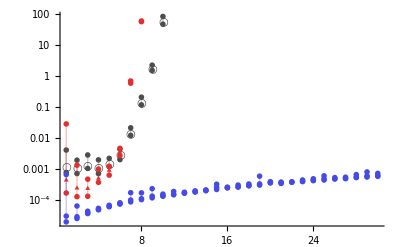

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{totalSymDummiesBuiltin,totalSymDummiesxPerm,totalSymDummiesImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

## Test 3: Randomized total symmetry

### Constructing totally symmetric split groups

```mathematica
Join[buildSymmetricGroup[Range[5]],buildSymmetricGroup[Range[6,10]]]
```

PermutationGroup[{System`Cycles[{{1,2}}],System`Cycles[{{2,3}}],System`Cycles[{{3,4}}],System`Cycles[{{4,5}}]},{System`Cycles[{{6,7}}],System`Cycles[{{7,8}}],System`Cycles[{{8,9}}],System`Cycles[{{9,10}}]}]

### Data for Mathematica built-in functions

```mathematica
Module[
{numindicesrange=Range[12],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,signedgens},
group=Join[buildSymmetricGroup[Range[#1]],buildSymmetricGroup[Range[#1+1,2*#1]]];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,2*#1],Reals,signedgens]}},
timings=Table[
With[{initialconfig=TensorContract[A,
Partition[RandomSample[Range[2*#1]],2]
]},
First@AbsoluteTiming@TensorReduce[initialconfig]
],
trialsperrun]];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/random-total-sym-dummies-builtin.data"
```

### Data for xPerm

```mathematica
Module[
{numindicesrange=Range[9],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets},
group=Join[buildSymmetricGroup[Range[#1]],buildSymmetricGroup[Range[#1+1,2*#1]]];
length=2*#1+2;
base=Range[length-2];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees={};
dummysetspec={2*#1};
dummysets=Flatten@{Range[2*#1]};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[2*#1],{length-1,length}]},
First@AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/random-total-sym-dummies-xperm.data"
```

### Data for improved BP

```mathematica
Module[
{numindicesrange=Range[1,30],
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,slotdata,subgroups,labeldata},
group=Join[buildSymmetricGroup[Range[#1]],buildSymmetricGroup[Range[#1+1,2*#1]]];
length=2*#1+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Join[ConstantArray[1,length-2],{length-1,length}],
Join[ConstantArray[2,length-2],{0,0}]
};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[2*#1],{length-1,length}]},
First@AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
{#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numindicesrange]
]>>"data/random-total-sym-dummies-improved.data"
```

### Generating plots

First let’s read in the data from the files:

```mathematica
randomTotalSymDummiesBuiltin=<<"data/random-total-sym-dummies-builtin.data";
randomTotalSymDummiesxPerm=<<"data/random-total-sym-dummies-xperm.data";
randomTotalSymDummiesImproved=<<"data/random-total-sym-dummies-improved.data";
```

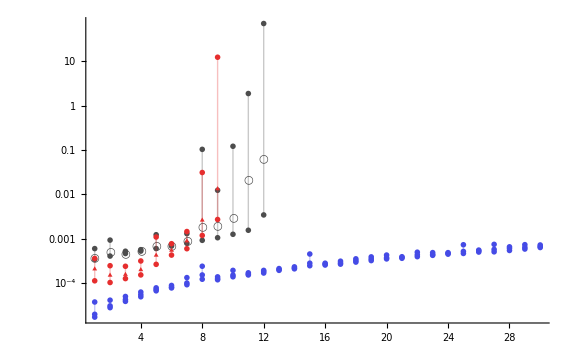

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{randomTotalSymDummiesBuiltin,randomTotalSymDummiesxPerm,randomTotalSymDummiesImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

## Test 4: Dummy indices with pairwise total symmetry

### Data for Mathematica built-in functions

```mathematica
Module[
{numblocksrange=Range[9],
blocksize=2,
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,signedgens,range},
range=blocksize*#1;
group=Join[
buildBlockSymmetricGroup[1,#1,blocksize],
buildBlockSymmetricGroup[1+range,#1,blocksize]
];
length=2*range+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,2*range],Reals,signedgens]}},
timings=Table[
With[{initialconfig=TensorContract[A,
Transpose[{RandomSample@Range[range],range+RandomSample@Range[range]}]
]},
First@AbsoluteTiming@TensorReduce[initialconfig]
],
trialsperrun]];
{2*blocksize*#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numblocksrange]
]>>"data/pairwise-sym-dummies-builtin.data"
```

### Data for xPerm

```mathematica
Module[
{numblocksrange=Range[7],
blocksize=2,
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets,range},
range=blocksize*#1;
group=Join[
buildBlockSymmetricGroup[1,#1,blocksize],
buildBlockSymmetricGroup[1+range,#1,blocksize]
];
length=2*range+2;
base=Range[length-2];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees={};
dummysetspec={2*range};
dummysets=Flatten@{Range[2*range]};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*range,2],
RandomSample@Range[2,2*range,2],{length-1,length}]},
First@AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
{2*blocksize*#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numblocksrange]
]>>"data/pairwise-sym-dummies-xperm.data"
```

### Data for improved BP

```mathematica
Module[
{numblocksrange=Range[8],
blocksize=2,
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,slotdata,subgroups,labeldata,range},
range=blocksize*#1;
group=Join[
buildBlockSymmetricGroup[1,#1,blocksize],
buildBlockSymmetricGroup[1+range,#1,blocksize]
];
length=2*range+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Join[ConstantArray[1,length-2],{length-1,length}],
Join[ConstantArray[2,length-2],{0,0}]
};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[1,2*range,2],
RandomSample@Range[2,2*range,2],{length-1,length}]},
First@AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
{2*blocksize*#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numblocksrange]
]>>"data/pairwise-sym-dummies-improved.data"
```

### Generating plots

First let’s read in the data from the files:

```mathematica
pairwiseSymDummiesBuiltin=<<"data/pairwise-sym-dummies-builtin.data";
pairwiseSymDummiesxPerm=<<"data/pairwise-sym-dummies-xperm.data";
pairwseSymDummiesImproved=<<"data/pairwise-sym-dummies-improved.data";
```

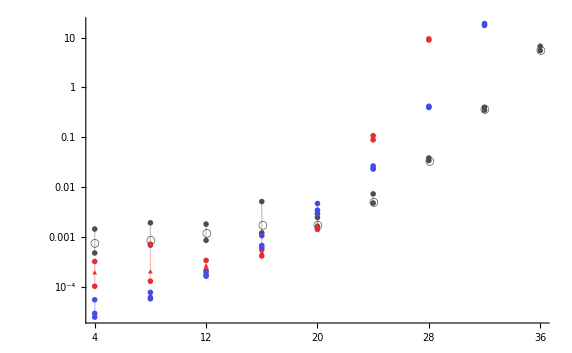

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{pairwiseSymDummiesBuiltin,pairwiseSymDummiesxPerm,pairwseSymDummiesImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]},
Ticks->{Range[4,36,4],Charting`ScaledTicks[{Log,Exp}]}
]
```

## Test 5: Randomized pairwise total symmetry

### Data for Mathematica built-in functions

```mathematica
Module[
{numblocksrange=Range[15],
blocksize=2,
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,signedgens,range},
range=blocksize*#1;
group=Join[
buildBlockSymmetricGroup[1,#1,blocksize],
buildBlockSymmetricGroup[1+range,#1,blocksize]
];
length=2*range+2;
generators=Sort@listifyGenerators[group,length];
signedgens=Map[{#[[1;;-3]],#[[-1]]-#[[-2]]}&,generators];
Block[{$Assumptions={A∈Arrays[ConstantArray[d,2*range],Reals,signedgens]}},
timings=Table[
With[{initialconfig=TensorContract[A,
Partition[RandomSample[Range[2*range]],2]
]},
First@AbsoluteTiming@TensorReduce[initialconfig]
],
trialsperrun]];
{2*blocksize*#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numblocksrange]
]>>"data/random-pairwise-sym-dummies-builtin.data"
```

### Data for xPerm

```mathematica
Module[
{numblocksrange=Range[11],
blocksize=2,
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,sgsswitch,base,frees,dummysetspec,dummysetsigns,dummysets,repeatsetspec,repeatsets,range},
range=blocksize*#1;
group=Join[
buildBlockSymmetricGroup[1,#1,blocksize],
buildBlockSymmetricGroup[1+range,#1,blocksize]
];
length=2*range+2;
base=Range[length-2];
generators=Flatten@Sort@listifyGenerators[group,length];
sgsswitch=1;
frees={};
dummysetspec={2*range};
dummysets=Flatten@{Range[2*range]};
dummysetsigns={1};
repeatsetspec={};
repeatsets=Flatten@{{}};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[2*range],{length-1,length}]},
First@AbsoluteTiming@
canonicalPerm[initialconfig,
length,sgsswitch,base,generators,frees,dummysetspec,dummysets,dummysetsigns,repeatsetspec,repeatsets]
],
trialsperrun];
{2*blocksize*#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numblocksrange]
]>>"data/random-pairwise-sym-dummies-xperm.data"
```

### Data for improved BP

```mathematica
Module[
{numblocksrange=Range[14],
blocksize=2,
trialsperrun=10},
Map[
(Block[{timings,group,length,generators,slotdata,subgroups,labeldata,range},
range=blocksize*#1;
group=Join[
buildBlockSymmetricGroup[1,#1,blocksize],
buildBlockSymmetricGroup[1+range,#1,blocksize]
];
length=2*range+2;
generators=Sort@listifyGenerators[group,length];
slotdata=If[Length[generators]>0,
buildCubeSchreierVector[generators],
{Array[0&,length]}];
subgroups=symmetricSubgroups[slotdata];
labeldata={
Join[ConstantArray[1,length-2],{length-1,length}],
Join[ConstantArray[2,length-2],{0,0}]
};
timings=Table[
With[{initialconfig=Join[RandomSample@Range[2*range],{length-1,length}]},
First@AbsoluteTiming@
improvedButlerPortugal[initialconfig,slotdata,subgroups,labeldata]
],
trialsperrun];
{2*blocksize*#1,Min[timings],GeometricMean[timings],Max[timings]}]
)&,
numblocksrange]
]>>"data/random-pairwise-sym-dummies-improved.data"
```

### Generating plots

First let’s read in the data from the files:

```mathematica
randomPairwiseSymDummiesBuiltin=<<"data/random-pairwise-sym-dummies-builtin.data";
randomPairwiseSymDummiesxPerm=<<"data/random-pairwise-sym-dummies-xperm.data";
randomPairwseSymDummiesImproved=<<"data/random-pairwise-sym-dummies-improved.data";
```

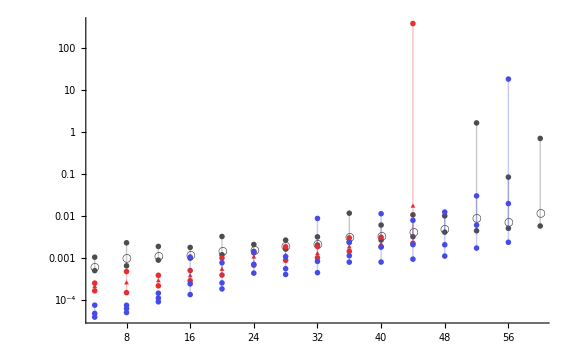

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{randomPairwiseSymDummiesBuiltin,randomPairwiseSymDummiesxPerm,randomPairwseSymDummiesImproved},
{GrayLevel[0.3],Hue[0.0,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}
]
```

## Best fit curves

### Symmetric frees

#### Read in data

```mathematica
symFreesBuiltin=<<"data/sym-frees-builtin.data";
symFreesxPerm=<<"data/sym-frees-xperm.data";
symFreesImproved=<<"data/sym-frees-improved.data";
```

#### Plot

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{symFreesBuiltin,symFreesxPerm,symFreesImproved},
{GrayLevel[0.3],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

#### Fit curves

```mathematica
logFitSymFreesBuiltin=Fit[MapAt[Log,
Select[symFreesBuiltin,#[[1]]≥100&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-17.2768+2.91025 Log[x]

```mathematica
logFitSymFreesxPerm=Fit[MapAt[Log,
Select[symFreesxPerm,#[[1]]≥100&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-21.502+3.64699 Log[x]

```mathematica
logFitSymFreesImproved=Fit[MapAt[Log,
Select[symFreesImproved,#[[1]]≥100&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-16.7955+2.53171 Log[x]

#### Plots

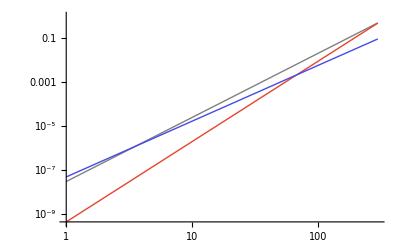

```mathematica
With[{curves=Exp@{logFitSymFreesBuiltin,logFitSymFreesxPerm,logFitSymFreesImproved}},
LogLogPlot[curves,{x,1,300},PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]]
```

```mathematica
Show[
Join[
MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{symFreesBuiltin,symFreesxPerm,symFreesImproved},
{GrayLevel[0.5],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
{With[{curves=Exp@{logFitSymFreesBuiltin,logFitSymFreesxPerm,logFitSymFreesImproved}},
LogPlot[curves,{x,1,300},
PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]
]}],
PlotRange->{Log[10^-5],Log[1.5]},AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

### Cyclic dummies

#### Read in data

```mathematica
cyclicDummiesBuiltin=<<"data/cyclic-dummies-builtin.data";
cyclicDummiesxPerm=<<"data/cyclic-dummies-xperm.data";
cyclicDummiesImproved=<<"data/cyclic-dummies-improved.data";
```

#### Plot

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{cyclicDummiesBuiltin,cyclicDummiesxPerm,cyclicDummiesImproved},
{GrayLevel[0.3],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

#### Fit curves

```mathematica
logFitBuiltin=Fit[MapAt[Log,
Select[cyclicDummiesBuiltin,#[[1]]≥50&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-17.7878+3.40301 Log[x]

```mathematica
logFitxPerm=Fit[MapAt[Log,
Select[cyclicDummiesxPerm,#[[1]]≥35&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-25.6791+6.47698 Log[x]

```mathematica
logFitImproved=Fit[MapAt[Log,
Select[cyclicDummiesImproved,#[[1]]≥50&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-15.6394+2.92366 Log[x]

#### Plots

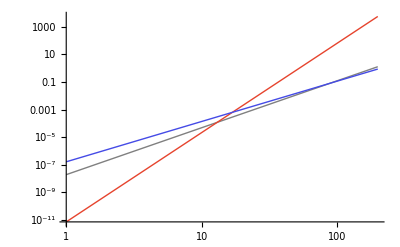

```mathematica
With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogLogPlot[curves,{x,1,200},PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]]
```

```mathematica
Show[
Join[
MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{cyclicDummiesBuiltin,cyclicDummiesxPerm,cyclicDummiesImproved},
{GrayLevel[0.5],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
{With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogPlot[curves,{x,1,200},
PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]
]}],
PlotRange->{Log[10^-5],Log[1.5]},AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

### No symmetry dummies

#### Read in data

```mathematica
noSymDummiesBuiltin=<<"data/no-sym-dummies-builtin.data";
noSymDummiesxPerm=<<"data/no-sym-dummies-xperm.data";
noSymDummiesImproved=<<"data/no-sym-dummies-improved.data";
```

#### Plot

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{noSymDummiesBuiltin,noSymDummiesxPerm,noSymDummiesImproved},
{GrayLevel[0.3],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

#### Fit curves

```mathematica
logFitBuiltin=Fit[MapAt[Log,
Select[noSymDummiesBuiltin,#[[1]]≥50&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-15.3223+2.67398 Log[x]

```mathematica
logFitxPerm=Fit[MapAt[Log,
Select[noSymDummiesxPerm,#[[1]]≥50&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-18.6912+3.56714 Log[x]

```mathematica
logFitImproved=Fit[MapAt[Log,
Select[noSymDummiesImproved,#[[1]]≥50&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-14.6623+1.83623 Log[x]

#### Plots

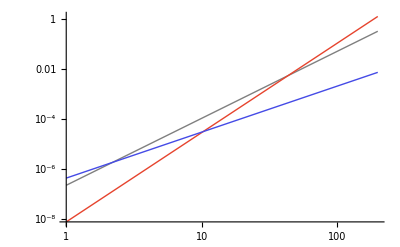

```mathematica
With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogLogPlot[curves,{x,1,200},PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]]
```

```mathematica
Show[
Join[
MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{noSymDummiesBuiltin,noSymDummiesxPerm,noSymDummiesImproved},
{GrayLevel[0.5],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
{With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogPlot[curves,{x,1,200},
PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]
]}],
PlotRange->{Log[10^-5],Log[1.5]},AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

### Nonzero Riemann tensors

#### Read in data

```mathematica
nonzeroRiemannsBuiltin=<<"data/nonzero-riemanns-builtin.data";
nonzeroRiemannsxPerm=<<"data/nonzero-riemanns-xperm.data";
nonzeroRiemannsImproved=<<"data/nonzero-riemanns-improved.data";
```

#### Plot

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{nonzeroRiemannsBuiltin,nonzeroRiemannsxPerm,nonzeroRiemannsImproved},
{GrayLevel[0.3],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

#### Fit curves

```mathematica
logFitBuiltin=Fit[MapAt[Log,
Select[nonzeroRiemannsBuiltin,#[[1]]≥20&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-15.8564+3.85796 Log[x]

```mathematica
logFitxPerm=Fit[MapAt[Log,
Select[nonzeroRiemannsxPerm,#[[1]]≥1&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-11.3518+3.09779 Log[x]

```mathematica
logFitImproved=Fit[MapAt[Log,
Select[nonzeroRiemannsImproved,#[[1]]≥20&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-11.9119+2.13765 Log[x]

#### Plots

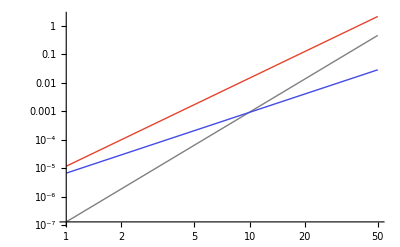

```mathematica
With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogLogPlot[curves,{x,1,50},PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]]
```

```mathematica
Show[
Join[
MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{nonzeroRiemannsBuiltin,nonzeroRiemannsxPerm,nonzeroRiemannsImproved},
{GrayLevel[0.5],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
{With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogPlot[curves,{x,1,50},
PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]
]}],
PlotRange->{Log[10^-5],Log[10]},AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

### Zero Riemann tensors

#### Read in data

```mathematica
zeroRiemannsBuiltin=<<"data/zero-riemanns-builtin.data";
zeroRiemannsxPerm=<<"data/zero-riemanns-xperm.data";
zeroRiemannsImproved=<<"data/zero-riemanns-improved.data";
```

#### Plot

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{zeroRiemannsBuiltin,zeroRiemannsxPerm,zeroRiemannsImproved},
{GrayLevel[0.3],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

#### Fit curves

```mathematica
logFitBuiltin=Fit[MapAt[Log,
Select[zeroRiemannsBuiltin,#[[1]]≥20&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-11.4606+2.22815 Log[x]

```mathematica
logFitxPerm=Fit[MapAt[Log,
Select[zeroRiemannsxPerm,#[[1]]≥10&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-13.5865+3.07944 Log[x]

```mathematica
logFitImproved=Fit[MapAt[Log,
Select[zeroRiemannsImproved,#[[1]]≥20&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-12.5769+1.12898 Log[x]

#### Plots

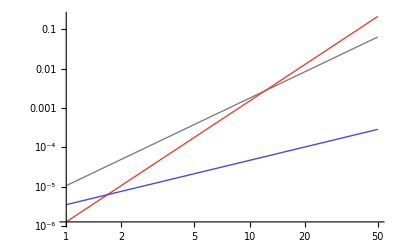

```mathematica
With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogLogPlot[curves,{x,1,50},PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]]
```

```mathematica
Show[
Join[
MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{zeroRiemannsBuiltin,zeroRiemannsxPerm,zeroRiemannsImproved},
{GrayLevel[0.5],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
{With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogPlot[curves,{x,1,50},
PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]
]}],
PlotRange->{Log[10^-5],Log[1]},AxesOrigin->{0,Log[10^-5]}]
```

-Graphics-

### Total symmetry

#### Read in data

```mathematica
totalSymDummiesBuiltin=<<"data/total-sym-dummies-builtin.data";
totalSymDummiesxPerm=<<"data/total-sym-dummies-xperm.data";
totalSymDummiesImproved=<<"data/total-sym-dummies-improved.data";
```

#### Plot

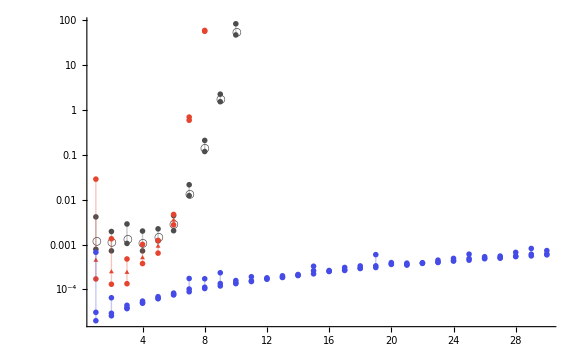

```mathematica
Show[MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{totalSymDummiesBuiltin,totalSymDummiesxPerm,totalSymDummiesImproved},
{GrayLevel[0.3],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
PlotRange->All,AxesOrigin->{0,Log[10^-5]}]
```

#### Fit curves

```mathematica
logFitBuiltin=Fit[MapAt[Log,
Select[totalSymDummiesBuiltin,#[[1]]≥1&][[All,{1,3}]],{All,2}],
{1,LogGamma[x+1],x,Log[x]},x]
```

5.22379-12.0343 x+12.0495 Log[x]+6.03967 LogGamma[1+x]

```mathematica
logFitxPerm=Fit[MapAt[Log,
Select[totalSymDummiesxPerm,#[[1]]≥1&][[All,{1,3}]],{All,2}],
{1,LogGamma[x+1],x,Log[x]},x]
```

11.9842-19.8498 x+18.1597 Log[x]+10.6491 LogGamma[1+x]

```mathematica
logFitImproved=Fit[MapAt[Log,
Select[totalSymDummiesImproved,#[[1]]≥10&][[All,{1,3}]],{All,2}],
{1,Log[x]},x]
```

-12.031+1.35908 Log[x]

#### Plots

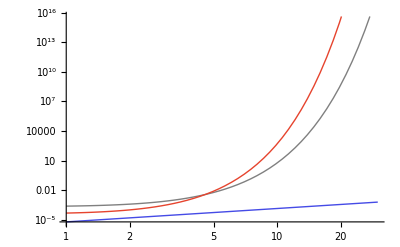

```mathematica
With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogLogPlot[curves,{x,1,30},PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]]
```

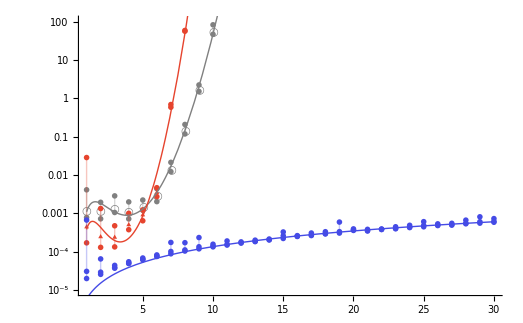

```mathematica
Show[
Join[
MapThread[buildListPlot[#1,ListLogPlot,#2,#3]&,
{{totalSymDummiesBuiltin,totalSymDummiesxPerm,totalSymDummiesImproved},
{GrayLevel[0.5],Hue[0.02,0.8,0.9],Hue[0.66,0.7,0.9]},
{"○",Style["▲",Larger],Style["•",Larger]}}],
{With[{curves=Exp@{logFitBuiltin,logFitxPerm,logFitImproved}},
LogPlot[curves,{x,1,30},
PlotStyle->{{GrayLevel[0.5],Thin},{Hue[0.02,0.8,0.9],Thin},{Hue[0.66,0.7,0.9],Thin}}]
]}],
PlotRange->{Log[10^-5],Log[100]},AxesOrigin->{0,Log[10^-5]}]
```

```mathematica
seconds=Exp@logFitBuiltin/.x->14.
minutes=seconds/60.;
hours=minutes/60.
days=hours/24.
years=days/365.24
```

9.6655×10^8

268486.

11186.9

30.629

### Random total symmetry

```mathematica
randomTotalSymDummiesBuiltin=<<"data/random-total-sym-dummies-builtin.data";
randomTotalSymDummiesxPerm=<<"data/random-total-sym-dummies-xperm.data";
randomTotalSymDummiesImproved=<<"data/random-total-sym-dummies-improved.data";
```

### Pairwise symmetry

```mathematica
pairwiseSymDummiesBuiltin=<<"data/pairwise-sym-dummies-builtin.data";
pairwiseSymDummiesxPerm=<<"data/pairwise-sym-dummies-xperm.data";
pairwseSymDummiesImproved=<<"data/pairwise-sym-dummies-improved.data";
```

### Random pairwise symmetry

```mathematica
randomPairwiseSymDummiesBuiltin=<<"data/random-pairwise-sym-dummies-builtin.data";
randomPairwiseSymDummiesxPerm=<<"data/random-pairwise-sym-dummies-xperm.data";
randomPairwseSymDummiesImproved=<<"data/random-pairwise-sym-dummies-improved.data";
```